# Numerische Berechnung von v_eff bei einer Magnetisierung M

Berechnung der Matrixelemente “veff * ρ = v < ν | τzσy |ν’ >” mit Magnetisierung M und μS für den Supraleiter und μN für den Normalleiter:

```mathematica
σx=τx=PauliMatrix[1];
σy=τy=PauliMatrix[2];
σz=τz=PauliMatrix[3];
σ0=τ0=IdentityMatrix[2];
σ0τ0=KroneckerProduct[τ0,σ0];
σxτz=KroneckerProduct[τz,σx];
σyτz=KroneckerProduct[τz,σy];
σxτy=KroneckerProduct[τy,σx];
σyτy=KroneckerProduct[τy,σy];
σzτy=KroneckerProduct[τy,σz];
τx11=KroneckerProduct[τx,σ0];
τy11=KroneckerProduct[τy,σ0];
τz11=KroneckerProduct[τz,σ0];
σz11=KroneckerProduct[τ0,σz];
```

```mathematica
$Assumptions=
ℏ>0&&v>0&&Δ>0&&L>0&&μ>0&&μSR>0&&μSL>0&&μN>0&&M>0 &&
ℏ∈Reals&&v∈Reals&&Δ∈Reals&&L∈Reals&&μ∈Reals&&μSR∈Reals&&μSL∈Reals&&μN∈Reals&&M∈Reals&&x∈Reals&&ϕ∈Reals&&ϵ∈Reals&&ϵ1∈Reals&&ϵ2∈Reals&&ϵ3∈Reals&&ϵ4∈Reals&&ϵr∈Reals&&ϵl∈Reals&&ϵ0∈Reals&&
ϵ<Δ ;
```

```mathematica
h0=FullSimplify[-ℏ*v*I*dx*σxτz-μ*τz11+M*σz11+Δ*(τx11*Cos[ϕ]+τy11*Sin[ϕ])]; (*allgemeines h0*)
hSR=FullSimplify[-ℏ*v*I*dx*σxτz-μSR*τz11+Δ*(τx11*Cos[ϕ]+τy11*Sin[ϕ])];(*h0 im Supraleiter (ohne M)*)
hSL=FullSimplify[-ℏ*v*I*dx*σxτz-μSL*τz11+Δ*(τx11*Cos[ϕ]+τy11*Sin[ϕ])]/.ϕ->0;(*h0 im Supraleiter (ohne M, ϕ=0)*)
hN=FullSimplify[-ℏ*v*I*dx*σxτz-μN*τz11+M*σz11];(*h0 im Normalleiter (mit M)*)
```

```mathematica
h1=-ℏ*v*I *dy*σyτz;
hGes=h0+h1;
MatrixForm[hGes]
```

(M-μ | -ⅈ dx v ℏ-dy v ℏ | ⅇ^(-ⅈ ϕ) Δ | 0
-ⅈ dx v ℏ+dy v ℏ | -M-μ | 0 | ⅇ^(-ⅈ ϕ) Δ
ⅇ^(ⅈ ϕ) Δ | 0 | M+μ | ⅈ dx v ℏ+dy v ℏ
0 | ⅇ^(ⅈ ϕ) Δ | ⅈ dx v ℏ-dy v ℏ | -M+μ)

Berechnung der Eigenvektoren von h0 im Ortsraum:

Berechnung im rechten Bereich mit μSR:

```mathematica
Mr=σxτz.(ϵr*σ0τ0+μSR*τz11-Δ*(τx11*Cos[ϕ]+τy11*Sin[ϕ]))/(-ℏ*v*I);
{λr,ξr}=FullSimplify[Eigensystem[Mr]]/.√(-Δ^2+ϵr^2)->ⅈ √(Δ^2-ϵr^2);
MatrixForm[Mr];
MatrixForm[λr];
MatrixForm[ξr];
ψr=FullSimplify[ξr*E^(λr*x)];
MatrixForm[ψr];
```

Überprüfen ob die Gleichung erfüllt ist:  ψ’-M*ψ = 0

```mathematica
FullSimplify[D[ψr[[1]],x]-Mr.ψr[[1]]]
```

{0,0,0,0}

Überprüfen ob ψ EV des Hamiltonians sind: H ψ = ϵ ψ

```mathematica
leftR=FullSimplify[hSR.ψr[[1]]/.dx->λr[[1]]];
MatrixForm[leftR];
rightR=ϵr*ψr[[1]];
MatrixForm[rightR];
FullSimplify[rightR-leftR]
```

{0,0,0,0}

Berechnung im linken Bereich mit μSL & ϕ=0:

```mathematica
Ml=σxτz.(ϵl*σ0τ0+μSL*τz11-Δ*(τx11*Cos[ϕ]+τy11*Sin[ϕ]))/(-ℏ*v*I)         /.ϕ->0;
{λl,ξl}=FullSimplify[Eigensystem[Ml]]/.√(-Δ^2+ϵl^2)->ⅈ √(Δ^2-ϵl^2);
MatrixForm[Ml];
MatrixForm[λl];
MatrixForm[ξl];
ψl=FullSimplify[ξl*E^(λl*x)];
MatrixForm[ψl];
```

Überprüfen ob die Gleichung erfüllt ist:  ψ’-M*ψ = 0

```mathematica
FullSimplify[D[ψr[[1]],x]-Mr.ψr[[1]]]
```

{0,0,0,0}

Überprüfen ob ψ EV des Hamiltonians sind: H ψ = ϵ ψ

```mathematica
leftL=FullSimplify[hSL.ψl[[1]]/.dx->λl[[1]]];
MatrixForm[leftL];
rightL=ϵl*ψl[[1]];
MatrixForm[rightL];
FullSimplify[rightL-leftL]
```

{0,0,0,0}

Berechnung im mittleren Bereich mit μN & ϕ=0 & Δ=0:

```mathematica
M0=σxτz.(ϵ0*σ0τ0+μN*τz11-M*σz11-Δ*(τx11*Cos[ϕ]+τy11*Sin[ϕ]))/(-ℏ*v*I)/.{ϕ->0,Δ->0};
{λ0,ξ0}=FullSimplify[Eigensystem[M0]];
MatrixForm[M0];
MatrixForm[λ0];
MatrixForm[ξ0];
ψ0=FullSimplify[ξ0*E^(λ0*x)];
MatrixForm[ψ0];
```

Überprüfen ob die Gleichung erfüllt ist:  ψ’-M*ψ = 0

```mathematica
FullSimplify[D[ψ0[[1]],x]-M0.ψ0[[1]]]
```

{0,0,0,0}

Überprüfen ob ψ EV des Hamiltonians sind: H ψ = ϵ ψ

```mathematica
left0=FullSimplify[hN.ψ0[[1]]/.dx->λ0[[1]]];
MatrixForm[left0];
right0=ϵ0*ψ0[[1]];
MatrixForm[right0];
FullSimplify[right0-left0]
```

{0,0,0,0}

Matrix aller EV hinschreiben und die propagierenden Lösungen entfernen

```mathematica
ψFull=ArrayFlatten[{
{Transpose[ψl]/.{ϵl->ϵ},Transpose[ψ0]/.{ϵ0->ϵ},Transpose[ψr]/.{ϵr->ϵ}}
}];
MatrixForm[ψFull]
```

((ⅇ^((x (√(Δ^2-ϵ^2)-ⅈ μSL))/(v ℏ)) (-ϵ-ⅈ √(Δ^2-ϵ^2)))/Δ | (ⅇ^((x (√(Δ^2-ϵ^2)+ⅈ μSL))/(v ℏ)) (ϵ-ⅈ √(Δ^2-ϵ^2)))/Δ | (ⅈ ⅇ^(-(x (√(Δ^2-ϵ^2)+ⅈ μSL))/(v ℏ)) (ⅈ ϵ+√(Δ^2-ϵ^2)))/Δ | (ⅇ^(-(x (√(Δ^2-ϵ^2)-ⅈ μSL))/(v ℏ)) (ϵ+ⅈ √(Δ^2-ϵ^2)))/Δ | (ⅈ ⅇ^((x √(M^2-(ϵ+μN)^2))/(v ℏ)) (M+ϵ+μN))/(√(M^2-(ϵ+μN)^2)) | -(ⅈ ⅇ^(-(x √(M^2-(ϵ+μN)^2))/(v ℏ)) (M+ϵ+μN))/(√(M^2-(ϵ+μN)^2)) | 0 | 0 | (ⅇ^(-ⅈ (ϕ+(x (ⅈ √((Δ-ϵ) (Δ+ϵ))+μSR))/(v ℏ))) (-ϵ-ⅈ √((Δ-ϵ) (Δ+ϵ))))/Δ | (ⅇ^((x √(Δ^2-ϵ^2)+ⅈ x μSR-ⅈ v ϕ ℏ)/(v ℏ)) (ϵ-ⅈ √((Δ-ϵ) (Δ+ϵ))))/Δ | (ⅇ^(-(x √((Δ-ϵ) (Δ+ϵ))+ⅈ (x μSR+v ϕ ℏ))/(v ℏ)) (-ϵ+ⅈ √((Δ-ϵ) (Δ+ϵ))))/Δ | (ⅇ^(-ⅈ (ϕ-(x (ⅈ √((Δ-ϵ) (Δ+ϵ))+μSR))/(v ℏ))) (ϵ+ⅈ √((Δ-ϵ) (Δ+ϵ))))/Δ
(ⅇ^((x (√(Δ^2-ϵ^2)-ⅈ μSL))/(v ℏ)) (ϵ+ⅈ √(Δ^2-ϵ^2)))/Δ | (ⅇ^((x (√(Δ^2-ϵ^2)+ⅈ μSL))/(v ℏ)) (ϵ-ⅈ √(Δ^2-ϵ^2)))/Δ | (ⅇ^(-(x (√(Δ^2-ϵ^2)+ⅈ μSL))/(v ℏ)) (ϵ-ⅈ √(Δ^2-ϵ^2)))/Δ | (ⅇ^(-(x (√(Δ^2-ϵ^2)-ⅈ μSL))/(v ℏ)) (ϵ+ⅈ √(Δ^2-ϵ^2)))/Δ | ⅇ^((x √(M^2-(ϵ+μN)^2))/(v ℏ)) | ⅇ^(-(x √(M^2-(ϵ+μN)^2))/(v ℏ)) | 0 | 0 | (ⅇ^(-ⅈ (ϕ+(x (ⅈ √((Δ-ϵ) (Δ+ϵ))+μSR))/(v ℏ))) (ϵ+ⅈ √((Δ-ϵ) (Δ+ϵ))))/Δ | (ⅇ^((x √(Δ^2-ϵ^2)+ⅈ x μSR-ⅈ v ϕ ℏ)/(v ℏ)) (ϵ-ⅈ √((Δ-ϵ) (Δ+ϵ))))/Δ | (ⅇ^(-(x √((Δ-ϵ) (Δ+ϵ))+ⅈ (x μSR+v ϕ ℏ))/(v ℏ)) (ϵ-ⅈ √((Δ-ϵ) (Δ+ϵ))))/Δ | (ⅇ^(-ⅈ (ϕ-(x (ⅈ √((Δ-ϵ) (Δ+ϵ))+μSR))/(v ℏ))) (ϵ+ⅈ √((Δ-ϵ) (Δ+ϵ))))/Δ
-ⅇ^((x (√(Δ^2-ϵ^2)-ⅈ μSL))/(v ℏ)) | ⅇ^((x (√(Δ^2-ϵ^2)+ⅈ μSL))/(v ℏ)) | -ⅇ^(-(x (√(Δ^2-ϵ^2)+ⅈ μSL))/(v ℏ)) | ⅇ^(-(x (√(Δ^2-ϵ^2)-ⅈ μSL))/(v ℏ)) | 0 | 0 | -(ⅈ ⅇ^((x √((M+ϵ-μN) (M-ϵ+μN)))/(v ℏ)) (M+ϵ-μN))/(√((M+ϵ-μN) (M-ϵ+μN))) | (ⅈ ⅇ^(-(x √((M+ϵ-μN) (M-ϵ+μN)))/(v ℏ)) (M+ϵ-μN))/(√((M+ϵ-μN) (M-ϵ+μN))) | -ⅇ^((x (√((Δ-ϵ) (Δ+ϵ))-ⅈ μSR))/(v ℏ)) | ⅇ^((x (√((Δ-ϵ) (Δ+ϵ))+ⅈ μSR))/(v ℏ)) | -ⅇ^(-(x (√((Δ-ϵ) (Δ+ϵ))+ⅈ μSR))/(v ℏ)) | ⅇ^(-(x (√((Δ-ϵ) (Δ+ϵ))-ⅈ μSR))/(v ℏ))
ⅇ^((x (√(Δ^2-ϵ^2)-ⅈ μSL))/(v ℏ)) | ⅇ^((x (√(Δ^2-ϵ^2)+ⅈ μSL))/(v ℏ)) | ⅇ^(-(x (√(Δ^2-ϵ^2)+ⅈ μSL))/(v ℏ)) | ⅇ^(-(x (√(Δ^2-ϵ^2)-ⅈ μSL))/(v ℏ)) | 0 | 0 | ⅇ^((x √((M+ϵ-μN) (M-ϵ+μN)))/(v ℏ)) | ⅇ^(-(x √((M+ϵ-μN) (M-ϵ+μN)))/(v ℏ)) | ⅇ^((x (√((Δ-ϵ) (Δ+ϵ))-ⅈ μSR))/(v ℏ)) | ⅇ^((x (√((Δ-ϵ) (Δ+ϵ))+ⅈ μSR))/(v ℏ)) | ⅇ^(-(x (√((Δ-ϵ) (Δ+ϵ))+ⅈ μSR))/(v ℏ)) | ⅇ^(-(x (√((Δ-ϵ) (Δ+ϵ))-ⅈ μSR))/(v ℏ)))

Betrachtung der einzelnen Vektoren, um die evaneszenten Wellen zu identifizieren:
Im linken Supraleiter müssen die Terme ⅇ^xsein, damit bei x → -∞ :  ψ → 0 :			Die Vektoren 3 und 4 fallen raus.
Im rechten Supraleiter müssen die Terme ⅇ^-xsein, damit bei x → ∞ :  ψ → 0 :		Die Vektoren 9 und 10 fallen raus.

```mathematica
ψFullReduced=Transpose[Delete[Transpose[ψFull],{{3},{4},{9},{10}}]]; 
MatrixForm[ψFullReduced]
```

((ⅇ^((x (√(Δ^2-ϵ^2)-ⅈ μSL))/(v ℏ)) (-ϵ-ⅈ √(Δ^2-ϵ^2)))/Δ | (ⅇ^((x (√(Δ^2-ϵ^2)+ⅈ μSL))/(v ℏ)) (ϵ-ⅈ √(Δ^2-ϵ^2)))/Δ | (ⅈ ⅇ^((x √(M^2-(ϵ+μN)^2))/(v ℏ)) (M+ϵ+μN))/(√(M^2-(ϵ+μN)^2)) | -(ⅈ ⅇ^(-(x √(M^2-(ϵ+μN)^2))/(v ℏ)) (M+ϵ+μN))/(√(M^2-(ϵ+μN)^2)) | 0 | 0 | (ⅇ^(-(x √((Δ-ϵ) (Δ+ϵ))+ⅈ (x μSR+v ϕ ℏ))/(v ℏ)) (-ϵ+ⅈ √((Δ-ϵ) (Δ+ϵ))))/Δ | (ⅇ^(-ⅈ (ϕ-(x (ⅈ √((Δ-ϵ) (Δ+ϵ))+μSR))/(v ℏ))) (ϵ+ⅈ √((Δ-ϵ) (Δ+ϵ))))/Δ
(ⅇ^((x (√(Δ^2-ϵ^2)-ⅈ μSL))/(v ℏ)) (ϵ+ⅈ √(Δ^2-ϵ^2)))/Δ | (ⅇ^((x (√(Δ^2-ϵ^2)+ⅈ μSL))/(v ℏ)) (ϵ-ⅈ √(Δ^2-ϵ^2)))/Δ | ⅇ^((x √(M^2-(ϵ+μN)^2))/(v ℏ)) | ⅇ^(-(x √(M^2-(ϵ+μN)^2))/(v ℏ)) | 0 | 0 | (ⅇ^(-(x √((Δ-ϵ) (Δ+ϵ))+ⅈ (x μSR+v ϕ ℏ))/(v ℏ)) (ϵ-ⅈ √((Δ-ϵ) (Δ+ϵ))))/Δ | (ⅇ^(-ⅈ (ϕ-(x (ⅈ √((Δ-ϵ) (Δ+ϵ))+μSR))/(v ℏ))) (ϵ+ⅈ √((Δ-ϵ) (Δ+ϵ))))/Δ
-ⅇ^((x (√(Δ^2-ϵ^2)-ⅈ μSL))/(v ℏ)) | ⅇ^((x (√(Δ^2-ϵ^2)+ⅈ μSL))/(v ℏ)) | 0 | 0 | -(ⅈ ⅇ^((x √((M+ϵ-μN) (M-ϵ+μN)))/(v ℏ)) (M+ϵ-μN))/(√((M+ϵ-μN) (M-ϵ+μN))) | (ⅈ ⅇ^(-(x √((M+ϵ-μN) (M-ϵ+μN)))/(v ℏ)) (M+ϵ-μN))/(√((M+ϵ-μN) (M-ϵ+μN))) | -ⅇ^(-(x (√((Δ-ϵ) (Δ+ϵ))+ⅈ μSR))/(v ℏ)) | ⅇ^(-(x (√((Δ-ϵ) (Δ+ϵ))-ⅈ μSR))/(v ℏ))
ⅇ^((x (√(Δ^2-ϵ^2)-ⅈ μSL))/(v ℏ)) | ⅇ^((x (√(Δ^2-ϵ^2)+ⅈ μSL))/(v ℏ)) | 0 | 0 | ⅇ^((x √((M+ϵ-μN) (M-ϵ+μN)))/(v ℏ)) | ⅇ^(-(x √((M+ϵ-μN) (M-ϵ+μN)))/(v ℏ)) | ⅇ^(-(x (√((Δ-ϵ) (Δ+ϵ))+ⅈ μSR))/(v ℏ)) | ⅇ^(-(x (√((Δ-ϵ) (Δ+ϵ))-ⅈ μSR))/(v ℏ)))

Matrix für die Stetigkeitsbedingung erstellen

```mathematica
stetigkeit=ArrayFlatten[{
{Transpose[ψl]/.{ϵl->ϵ,x->-L},Transpose[ψ0]/.{ϵ0->ϵ,x->-L},0},
{0,Transpose[ψ0]/.{ϵ0->ϵ,x->L},Transpose[ψr]/.{ϵr->ϵ,x->L}}
}];
stetigkeitReduced=Transpose[Delete[Transpose[stetigkeit],{{3},{4},{9},{10}}]]; 
MatrixForm[stetigkeitReduced]
```

((ⅇ^(-(L (√(Δ^2-ϵ^2)-ⅈ μSL))/(v ℏ)) (-ϵ-ⅈ √(Δ^2-ϵ^2)))/Δ | (ⅇ^(-(L (√(Δ^2-ϵ^2)+ⅈ μSL))/(v ℏ)) (ϵ-ⅈ √(Δ^2-ϵ^2)))/Δ | (ⅈ ⅇ^(-(L √(M^2-(ϵ+μN)^2))/(v ℏ)) (M+ϵ+μN))/(√(M^2-(ϵ+μN)^2)) | -(ⅈ ⅇ^((L √(M^2-(ϵ+μN)^2))/(v ℏ)) (M+ϵ+μN))/(√(M^2-(ϵ+μN)^2)) | 0 | 0 | 0 | 0
(ⅇ^(-(L (√(Δ^2-ϵ^2)-ⅈ μSL))/(v ℏ)) (ϵ+ⅈ √(Δ^2-ϵ^2)))/Δ | (ⅇ^(-(L (√(Δ^2-ϵ^2)+ⅈ μSL))/(v ℏ)) (ϵ-ⅈ √(Δ^2-ϵ^2)))/Δ | ⅇ^(-(L √(M^2-(ϵ+μN)^2))/(v ℏ)) | ⅇ^((L √(M^2-(ϵ+μN)^2))/(v ℏ)) | 0 | 0 | 0 | 0
-ⅇ^(-(L (√(Δ^2-ϵ^2)-ⅈ μSL))/(v ℏ)) | ⅇ^(-(L (√(Δ^2-ϵ^2)+ⅈ μSL))/(v ℏ)) | 0 | 0 | -(ⅈ ⅇ^(-(L √((M+ϵ-μN) (M-ϵ+μN)))/(v ℏ)) (M+ϵ-μN))/(√((M+ϵ-μN) (M-ϵ+μN))) | (ⅈ ⅇ^((L √((M+ϵ-μN) (M-ϵ+μN)))/(v ℏ)) (M+ϵ-μN))/(√((M+ϵ-μN) (M-ϵ+μN))) | 0 | 0
ⅇ^(-(L (√(Δ^2-ϵ^2)-ⅈ μSL))/(v ℏ)) | ⅇ^(-(L (√(Δ^2-ϵ^2)+ⅈ μSL))/(v ℏ)) | 0 | 0 | ⅇ^(-(L √((M+ϵ-μN) (M-ϵ+μN)))/(v ℏ)) | ⅇ^((L √((M+ϵ-μN) (M-ϵ+μN)))/(v ℏ)) | 0 | 0
0 | 0 | (ⅈ ⅇ^((L √(M^2-(ϵ+μN)^2))/(v ℏ)) (M+ϵ+μN))/(√(M^2-(ϵ+μN)^2)) | -(ⅈ ⅇ^(-(L √(M^2-(ϵ+μN)^2))/(v ℏ)) (M+ϵ+μN))/(√(M^2-(ϵ+μN)^2)) | 0 | 0 | (ⅇ^(-(L √((Δ-ϵ) (Δ+ϵ))+ⅈ (L μSR+v ϕ ℏ))/(v ℏ)) (-ϵ+ⅈ √((Δ-ϵ) (Δ+ϵ))))/Δ | (ⅇ^(-ⅈ (ϕ-(L (ⅈ √((Δ-ϵ) (Δ+ϵ))+μSR))/(v ℏ))) (ϵ+ⅈ √((Δ-ϵ) (Δ+ϵ))))/Δ
0 | 0 | ⅇ^((L √(M^2-(ϵ+μN)^2))/(v ℏ)) | ⅇ^(-(L √(M^2-(ϵ+μN)^2))/(v ℏ)) | 0 | 0 | (ⅇ^(-(L √((Δ-ϵ) (Δ+ϵ))+ⅈ (L μSR+v ϕ ℏ))/(v ℏ)) (ϵ-ⅈ √((Δ-ϵ) (Δ+ϵ))))/Δ | (ⅇ^(-ⅈ (ϕ-(L (ⅈ √((Δ-ϵ) (Δ+ϵ))+μSR))/(v ℏ))) (ϵ+ⅈ √((Δ-ϵ) (Δ+ϵ))))/Δ
0 | 0 | 0 | 0 | -(ⅈ ⅇ^((L √((M+ϵ-μN) (M-ϵ+μN)))/(v ℏ)) (M+ϵ-μN))/(√((M+ϵ-μN) (M-ϵ+μN))) | (ⅈ ⅇ^(-(L √((M+ϵ-μN) (M-ϵ+μN)))/(v ℏ)) (M+ϵ-μN))/(√((M+ϵ-μN) (M-ϵ+μN))) | -ⅇ^(-(L (√((Δ-ϵ) (Δ+ϵ))+ⅈ μSR))/(v ℏ)) | ⅇ^(-(L (√((Δ-ϵ) (Δ+ϵ))-ⅈ μSR))/(v ℏ))
0 | 0 | 0 | 0 | ⅇ^((L √((M+ϵ-μN) (M-ϵ+μN)))/(v ℏ)) | ⅇ^(-(L √((M+ϵ-μN) (M-ϵ+μN)))/(v ℏ)) | ⅇ^(-(L (√((Δ-ϵ) (Δ+ϵ))+ⅈ μSR))/(v ℏ)) | ⅇ^(-(L (√((Δ-ϵ) (Δ+ϵ))-ⅈ μSR))/(v ℏ)))

Aus den Stetigkeitsbedingungen jetzt die Relation ϵ(ϕ) bzw. ϕ(ϵ) bestimmen durch Det = 0

```mathematica
DetStetigkeit=FullSimplify[Det[stetigkeitReduced]];
Det0=FullSimplify[Det[stetigkeitReduced]/(1/(Δ^2 ((M-ϵ)^2-μN^2))8 ⅇ^(-ⅈ ϕ-(2 L (2 √((Δ-ϵ) (Δ+ϵ))+√((M+ϵ-μN) (M-ϵ+μN))+√(M^2-(ϵ+μN)^2)))/(v ℏ)))] (*es wird durch "ungefähr" den Faktor vor der Determinante geteilt -> sinh & cosh*)
```

-((-1+ⅇ^((4 L √((M+ϵ-μN) (M-ϵ+μN)))/(v ℏ))) (-1+ⅇ^((4 L √((M-ϵ-μN) (M+ϵ+μN)))/(v ℏ))) M^2 Δ^2)-2 ⅇ^((2 L (√((M+ϵ-μN) (M-ϵ+μN))+√((M-ϵ-μN) (M+ϵ+μN))))/(v ℏ)) (-2 Δ^2 √((M+ϵ-μN) (M-ϵ+μN)) √((M-ϵ-μN) (M+ϵ+μN)) Cos[ϕ]-(Δ^2-2 ϵ^2) (ϵ^2-μN^2+√((M+ϵ-μN) (M-ϵ+μN)) √((M-ϵ-μN) (M+ϵ+μN))) Cosh[(2 L (-√((M+ϵ-μN) (M-ϵ+μN))+√((M-ϵ-μN) (M+ϵ+μN))))/(v ℏ)]+(Δ^2-2 ϵ^2) (ϵ^2-μN^2-√((M+ϵ-μN) (M-ϵ+μN)) √((M-ϵ-μN) (M+ϵ+μN))) Cosh[(2 L (√((M+ϵ-μN) (M-ϵ+μN))+√((M-ϵ-μN) (M+ϵ+μN))))/(v ℏ)]+2 ϵ √((Δ-ϵ) (Δ+ϵ)) ((ϵ (√((M+ϵ-μN) (M-ϵ+μN))-√((M-ϵ-μN) (M+ϵ+μN)))+μN (√((M+ϵ-μN) (M-ϵ+μN))+√((M-ϵ-μN) (M+ϵ+μN)))) Sinh[(2 L (-√((M+ϵ-μN) (M-ϵ+μN))+√((M-ϵ-μN) (M+ϵ+μN))))/(v ℏ)]+(μN (√((M+ϵ-μN) (M-ϵ+μN))-√((M-ϵ-μN) (M+ϵ+μN)))+ϵ (√((M+ϵ-μN) (M-ϵ+μN))+√((M-ϵ-μN) (M+ϵ+μN)))) Sinh[(2 L (√((M+ϵ-μN) (M-ϵ+μN))+√((M-ϵ-μN) (M+ϵ+μN))))/(v ℏ)]))

```mathematica
cosϕ1=FullSimplify[Solve[Det0==0,Cos[ϕ]]]
```

{{Cos[ϕ]→1/(2 Δ^2 √((M+ϵ-μN) (M-ϵ+μN)) √(M^2-(ϵ+μN)^2))(-((Δ^2-2 ϵ^2) (ϵ^2-μN^2+√((M+ϵ-μN) (M-ϵ+μN)) √(M^2-(ϵ+μN)^2)) Cosh[(2 L (√((M+ϵ-μN) (M-ϵ+μN))-√(M^2-(ϵ+μN)^2)))/(v ℏ)])+(Δ^2-2 ϵ^2) (ϵ^2-μN^2-√((M+ϵ-μN) (M-ϵ+μN)) √(M^2-(ϵ+μN)^2)) Cosh[(2 L (√((M+ϵ-μN) (M-ϵ+μN))+√(M^2-(ϵ+μN)^2)))/(v ℏ)]+2 M^2 Δ^2 Sinh[(2 L √((M+ϵ-μN) (M-ϵ+μN)))/(v ℏ)] Sinh[(2 L √(M^2-(ϵ+μN)^2))/(v ℏ)]+2 ϵ √((Δ-ϵ) (Δ+ϵ)) (-((ϵ √((M+ϵ-μN) (M-ϵ+μN))+μN √((M+ϵ-μN) (M-ϵ+μN))-ϵ √(M^2-(ϵ+μN)^2)+μN √(M^2-(ϵ+μN)^2)) Sinh[(2 L (√((M+ϵ-μN) (M-ϵ+μN))-√(M^2-(ϵ+μN)^2)))/(v ℏ)])+(ϵ √((M+ϵ-μN) (M-ϵ+μN))+μN √((M+ϵ-μN) (M-ϵ+μN))+ϵ √(M^2-(ϵ+μN)^2)-μN √(M^2-(ϵ+μN)^2)) Sinh[(2 L (√((M+ϵ-μN) (M-ϵ+μN))+√(M^2-(ϵ+μN)^2)))/(v ℏ)]))}}

```mathematica
detStep1=FullSimplify[(Normal[Flatten[Values[cosϕ1]][[1]]]/.{√((M+ϵ-μN) (M-ϵ+μN))->ⅈ √((-M-ϵ+μN) (M-ϵ+μN)),√(M^2-(ϵ+μN)^2)->ⅈ √((ϵ+μN)^2-M^2)})/.{√((-M-ϵ+μN) (M-ϵ+μN))->a,√((ϵ+μN)^2-M^2)->b}]
```

((Δ^2-2 ϵ^2) (a b-ϵ^2+μN^2) Cos[(2 (a-b) L)/(v ℏ)]+(Δ^2-2 ϵ^2) (a b+ϵ^2-μN^2) Cos[(2 (a+b) L)/(v ℏ)]-2 M^2 Δ^2 Sin[(2 a L)/(v ℏ)] Sin[(2 b L)/(v ℏ)]+2 ϵ √((Δ-ϵ) (Δ+ϵ)) (((a-b) ϵ+(a+b) μN) Sin[(2 (a-b) L)/(v ℏ)]-((a+b) ϵ+(a-b) μN) Sin[(2 (a+b) L)/(v ℏ)]))/(2 Δ^2 √((M+ϵ-μN) (M-ϵ+μN)) √(M^2-(ϵ+μN)^2))

```mathematica
detStep2=1/(-2 Δ^2 a b)((Δ^2-2 ϵ^2) (a b-ϵ^2+μN^2) Cos[(2 (a-b) L)/(v ℏ)]+(Δ^2-2 ϵ^2) (a b+ϵ^2-μN^2) Cos[(2 (a+b) L)/(v ℏ)]-2 M^2 Δ^2 Sin[(2 a L)/(v ℏ)] Sin[(2 b L)/(v ℏ)]+2 ϵ √((Δ-ϵ) (Δ+ϵ)) (((a-b) ϵ+(a+b) μN) Sin[(2 (a-b) L)/(v ℏ)]-((a+b) ϵ+(a-b) μN) Sin[(2 (a+b) L)/(v ℏ)]));
```

```mathematica
(*
a=√((-M-ϵ+μN) (M-ϵ+μN))=√(((-ϵ+μN)-M) ((-ϵ+μN)+M))=√((μN-ϵ)^2-M^2);
b=√((μN+ϵ)^2-M^2);
*)
```

```mathematica
detStep3=detStep2/.{a->√((μN-ϵ)^2-M^2),b->√((μN+ϵ)^2-M^2)}
```

-1/(2 Δ^2 √(-M^2+(-ϵ+μN)^2) √(-M^2+(ϵ+μN)^2))((Δ^2-2 ϵ^2) (-ϵ^2+μN^2+√(-M^2+(-ϵ+μN)^2) √(-M^2+(ϵ+μN)^2)) Cos[(2 L (√(-M^2+(-ϵ+μN)^2)-√(-M^2+(ϵ+μN)^2)))/(v ℏ)]+(Δ^2-2 ϵ^2) (ϵ^2-μN^2+√(-M^2+(-ϵ+μN)^2) √(-M^2+(ϵ+μN)^2)) Cos[(2 L (√(-M^2+(-ϵ+μN)^2)+√(-M^2+(ϵ+μN)^2)))/(v ℏ)]-2 M^2 Δ^2 Sin[(2 L √(-M^2+(-ϵ+μN)^2))/(v ℏ)] Sin[(2 L √(-M^2+(ϵ+μN)^2))/(v ℏ)]+2 ϵ √((Δ-ϵ) (Δ+ϵ)) ((ϵ (√(-M^2+(-ϵ+μN)^2)-√(-M^2+(ϵ+μN)^2))+μN (√(-M^2+(-ϵ+μN)^2)+√(-M^2+(ϵ+μN)^2))) Sin[(2 L (√(-M^2+(-ϵ+μN)^2)-√(-M^2+(ϵ+μN)^2)))/(v ℏ)]-(μN (√(-M^2+(-ϵ+μN)^2)-√(-M^2+(ϵ+μN)^2))+ϵ (√(-M^2+(-ϵ+μN)^2)+√(-M^2+(ϵ+μN)^2))) Sin[(2 L (√(-M^2+(-ϵ+μN)^2)+√(-M^2+(ϵ+μN)^2)))/(v ℏ)]))

```mathematica
cosϕ[ϵ_,L_,M_,Δ_,μN_,v_,ℏ_]:=Evaluate[detStep3];
cosϕ[0.1,1,1.2,1,1,1,1]
```

-0.0135433+0. ⅈ

Plotten

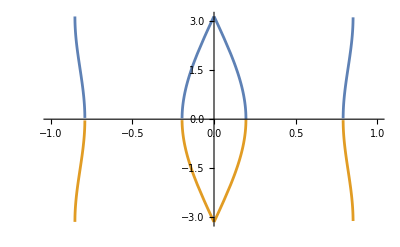

```mathematica
Mvalue=1;

Plot[Evaluate[{ArcCos[cosϕ[ϵ,1,Mvalue,1,1,1,1]],-ArcCos[cosϕ[ϵ,1,Mvalue,1,1,1,1]]}],{ϵ,-1,1}]
```

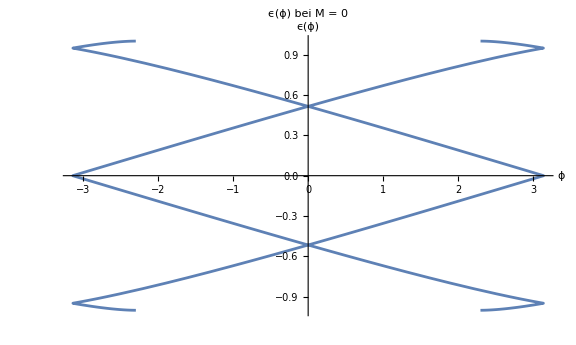

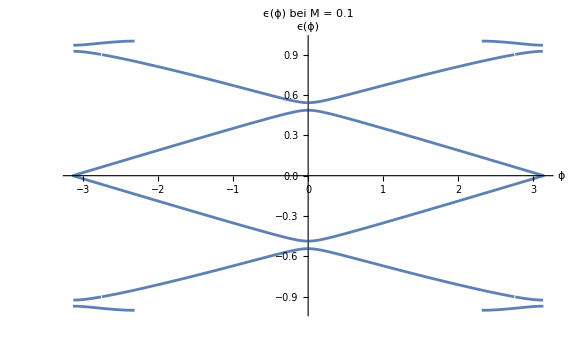

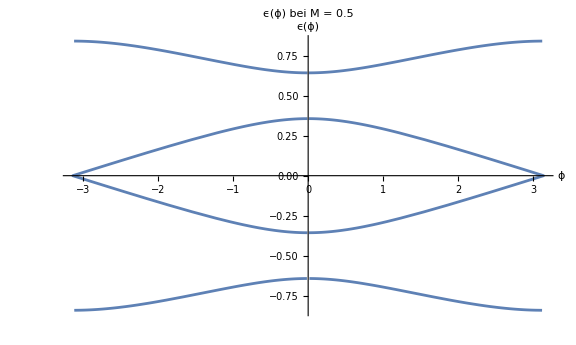

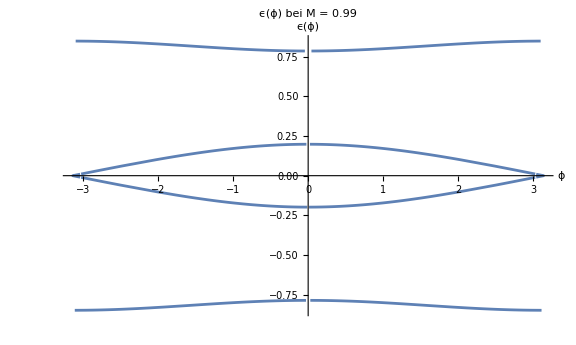

```mathematica
MagnetisierungTests={0,0.1,0.5,0.99};

PlotsM={};
For[i=1,i<=Length[MagnetisierungTests],i++,
plot=ParametricPlot[Evaluate[
{{ArcCos[cosϕ[ϵ,1,MagnetisierungTests[[i]],1,1,1,1]],ϵ},
{-ArcCos[cosϕ[ϵ,1,MagnetisierungTests[[i]],1,1,1,1]],ϵ}}],
{ϵ,-1,1},PlotRange->All,AxesLabel->{"ϕ","ϵ(ϕ)"},PlotLabel->"ϵ(ϕ) bei M = "<>ToString[MagnetisierungTests[[i]]],ImageSize->Large,AspectRatio->0.6,PlotStyle->RGBColor[0.368417, 0.506779, 0.709798]];
AppendTo[PlotsM,plot]
Print[plot]
]
(*GraphicsRow[PlotsM,ImageSize->Full]*)
```

Berechnung der Koeffizienten für die Wellenfunktionen aus den Stetigkeitsbedingungen

```mathematica
Det[(stetigkeitReduced/.{ϕ->ArcCos[cosϕ[ϵ,L,M,Δ,μN,v,ℏ]]})/.{L->1,v->1,ϵ->0.1,Δ->1,ℏ->1,M->1,μN->1,μSR->1,μSL->1}]
zwischenSchrittEigensys[ϵ_,L_,M_,Δ_,μN_,μSL_,μSR_,v_,ℏ_]:=Evaluate[stetigkeitReduced/.{ϕ->ArcCos[cosϕ[ϵ,L,M,Δ,μN,v,ℏ]]}];
eigensys[ϵ_,L_,M_,Δ_,μN_,μSL_,μSR_,v_,ℏ_]:=Eigensystem[zwischenSchrittEigensys[ϵ,L,M,Δ,μN,μSL,μSR,v,ℏ]];
Text["Es werden Eigenvektoren zum EW 0 gesucht:"]
Last[eigensys[0.1,1,1,1,1,1,1,1,1][[1]]]
Text["Der EV zum EW 0, der die Vorfaktoren der Wellenfunktionen beinhaltet, ist:"]
vorfaktoren[ϵ_,L_,M_,Δ_,μN_,μSL_,μSR_,v_,ℏ_]:=Last[eigensys[ϵ,L,M,Δ,μN,μSL,μSR,v,ℏ][[2]]];
MatrixForm[vorfaktoren[0.1,1,1,1,1,1,1,1,1]]
```

Det::luc: Result for Det of badly conditioned matrix {{0.289579-0.229875 ⅈ,-0.289579-0.229875 ⅈ,4.10977-2.02727 ⅈ,-4.10977-2.02727 ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{-0.289579+0.229875 ⅈ,-0.289579-0.229875 ⅈ,0.896825-0.442386 ⅈ,0.896825+0.442386 ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{-0.199765-0.311115 ⅈ,0.199765-0.311115 ⅈ,«4»,0.+0. ⅈ,0.+0. ⅈ},«1»,«1»,{«1»},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-0.354754 ⅈ,0.+0.148361 ⅈ,-0.199765+0.311115 ⅈ,0.199765+0.311115 ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,1.54634+0. ⅈ,0.646689+0. ⅈ,0.199765-0.311115 ⅈ,0.199765+0.311115 ⅈ}} may contain significant numerical errors.

2.04241×10^-16-7.51773×10^-17 ⅈ

Es werden Eigenvektoren zum EW 0 gesucht:

5.89825×10^-16+1.69985×10^-15 ⅈ

Der EV zum EW 0, der die Vorfaktoren der Wellenfunktionen beinhaltet, ist:

(0.12668-0.345778 ⅈ
0.176698+0.522403 ⅈ
-0.0820107+0.0335428 ⅈ
-0.0491861+0.0201174 ⅈ
0.0107065-0.234116 ⅈ
-0.218343+0.0851548 ⅈ
-0.286959+0.230791 ⅈ
0.551477+0. ⅈ)

Heaviside-Funktionen für einzelnen Wellenfunktionen in den Teilbereichen:

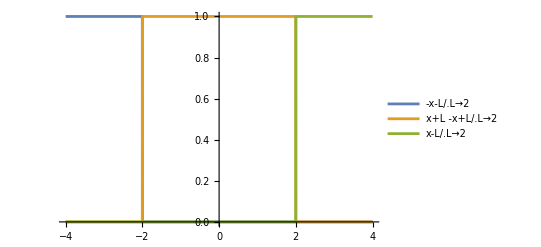

```mathematica
Plot[{
HeavisideTheta[-x-L]                                                                      /.L->2,
HeavisideTheta[x+L] HeavisideTheta[-x+L]                       /.L->2,
HeavisideTheta[x-L]                                                                        /.L->2
},{x,-4,4},PlotLegends->"Expressions"]
```

Wellenfunktionen zusammensetzten

```mathematica
HeavisideThetavektor[x_,L_]:=({{HeavisideTheta[-x-L]}, {HeavisideTheta[-x-L]}, {HeavisideTheta[x+L] HeavisideTheta[-x+L]}, {HeavisideTheta[x+L] HeavisideTheta[-x+L]}, {HeavisideTheta[x+L] HeavisideTheta[-x+L]}, {HeavisideTheta[x+L] HeavisideTheta[-x+L]}, {HeavisideTheta[x-L]}, {HeavisideTheta[x-L]}});
ψFullReducedFunc[x_,ϵ_,L_,M_,Δ_,μN_,μSL_,μSR_,v_,ℏ_]:=Evaluate[ψFullReduced/.{ϕ->ArcCos[cosϕ[ϵ,L,M,Δ,μN,v,ℏ]]}];
```

```mathematica
σ1[x_,ϵ_,L_,M_,Δ_,μN_,μSL_,μSR_,v_,ℏ_]:=ψFullReducedFunc[x,ϵ,L,M,Δ,μN,μSL,μSR,v,ℏ].(vorfaktoren[ϵ,L,M,Δ,μN,μSL,μSR,v,ℏ]*HeavisideThetavektor[x,L]);
σ2[x_,ϵ_,L_,M_,Δ_,μN_,μSL_,μSR_,v_,ℏ_]:=ψFullReducedFunc[x,-ϵ,L,M,Δ,μN,μSL,μSR,v,ℏ].(vorfaktoren[-ϵ,L,M,Δ,μN,μSL,μSR,v,ℏ]*HeavisideThetavektor[x,L]);
MatrixForm[σ1[1.5,0.1,1,1,1,1,1,1,1,1]]
MatrixForm[σ2[1.5,-0.1,1,1,1,1,1,1,1,1]]
```

(0.13983+0.148515 ⅈ
0.00450454+0.0531071 ⅈ
-0.0384218+0.0556483 ⅈ
0.0559618+0.19169 ⅈ)

(0.13983+0.148515 ⅈ
0.00450454+0.0531071 ⅈ
-0.0384218+0.0556483 ⅈ
0.0559618+0.19169 ⅈ)

```mathematica
σ1Conj[x_,ϵ_,L_,M_,Δ_,μN_,μSL_,μSR_,v_,ℏ_]:=Conjugate[σ1[x,ϵ,L,M,Δ,μN,μSL,μSR,v,ℏ]];
σ2Conj[x_,ϵ_,L_,M_,Δ_,μN_,μSL_,μSR_,v_,ℏ_]:=Conjugate[σ2[x,ϵ,L,M,Δ,μN,μSL,μSR,v,ℏ]];
MatrixForm[σ1Conj[1.5,0.1,1,1,1,1,1,1,1,1]]
MatrixForm[σ2Conj[1.5,-0.1,1,1,1,1,1,1,1,1]]
```

(0.13983-0.148515 ⅈ
0.00450454-0.0531071 ⅈ
-0.0384218-0.0556483 ⅈ
0.0559618-0.19169 ⅈ)

(0.13983-0.148515 ⅈ
0.00450454-0.0531071 ⅈ
-0.0384218-0.0556483 ⅈ
0.0559618-0.19169 ⅈ)

Wellenfunktionen normieren (numerisch):

```mathematica
NNormFactorσ1[ϵ_,L_,M_,Δ_,μN_,μSL_,μSR_,v_,ℏ_]:=Sqrt[1/NIntegrate[(σ1Conj[x,ϵ,L,M,Δ,μN,μSL,μSR,v,ℏ].σ1[x,ϵ,L,M,Δ,μN,μSL,μSR,v,ℏ]),{x,-50,50},PrecisionGoal->4,AccuracyGoal->4]];
NNormFactorσ2[ϵ_,L_,M_,Δ_,μN_,μSL_,μSR_,v_,ℏ_]:=Sqrt[1/NIntegrate[(σ2Conj[x,ϵ,L,M,Δ,μN,μSL,μSR,v,ℏ].σ2[x,ϵ,L,M,Δ,μN,μSL,μSR,v,ℏ]),{x,-50,50},PrecisionGoal->4,AccuracyGoal->4]];
NNormFactorσ1[0.1,1,1,1,1,1,1,1,1]
NNormFactorσ2[-0.1,1,1,1,1,1,1,1,1]
```

1.33329

1.33329

```mathematica
Nσ1[x_,ϵ_,L_,M_,Δ_,μN_,μSL_,μSR_,v_,ℏ_]:=NNormFactorσ1[ϵ,L,M,Δ,μN,μSL,μSR,v,ℏ]*σ1[x,ϵ,L,M,Δ,μN,μSL,μSR,v,ℏ];
Nσ2[x_,ϵ_,L_,M_,Δ_,μN_,μSL_,μSR_,v_,ℏ_]:=NNormFactorσ2[ϵ,L,M,Δ,μN,μSL,μSR,v,ℏ]*σ2[x,ϵ,L,M,Δ,μN,μSL,μSR,v,ℏ];
Nσ1Conj[x_,ϵ_,L_,M_,Δ_,μN_,μSL_,μSR_,v_,ℏ_]:=NNormFactorσ1[ϵ,L,M,Δ,μN,μSL,μSR,v,ℏ]*σ1Conj[x,ϵ,L,M,Δ,μN,μSL,μSR,v,ℏ];
Nσ2Conj[x_,ϵ_,L_,M_,Δ_,μN_,μSL_,μSR_,v_,ℏ_]:=NNormFactorσ2[ϵ,L,M,Δ,μN,μSL,μSR,v,ℏ]*σ2Conj[x,ϵ,L,M,Δ,μN,μSL,μSR,v,ℏ];

MatrixForm[Nσ1Conj[1.5,0.1,1,1,1,1,1,1,1,1]]
MatrixForm[Nσ2Conj[1.5,-0.1,1,1,1,1,1,1,1,1]]
```

(0.186434-0.198014 ⅈ
0.00600587-0.0708073 ⅈ
-0.0512274-0.0741954 ⅈ
0.0746133-0.255579 ⅈ)

(0.186434-0.198014 ⅈ
0.00600587-0.0708073 ⅈ
-0.0512274-0.0741954 ⅈ
0.0746133-0.255579 ⅈ)

Normierung überprüfen:

```mathematica
NNormTestingσ1[ϵ_,L_,M_,Δ_,μN_,μSL_,μSR_,v_,ℏ_]:=NIntegrate[(Nσ1Conj[x,ϵ,L,M,Δ,μN,μSL,μSR,v,ℏ].Nσ1[x,ϵ,L,M,Δ,μN,μSL,μSR,v,ℏ]),{x,-50,50},PrecisionGoal->4,AccuracyGoal->4];
NNormTestingσ2[ϵ_,L_,M_,Δ_,μN_,μSL_,μSR_,v_,ℏ_]:=NIntegrate[(Nσ2Conj[x,ϵ,L,M,Δ,μN,μSL,μSR,v,ℏ].Nσ2[x,ϵ,L,M,Δ,μN,μSL,μSR,v,ℏ]),{x,-50,50},PrecisionGoal->4,AccuracyGoal->4];
NNormTestingσ1[0.1,1,1,1,1,1,1,1,1]
NNormTestingσ2[0.1,1,1,1,1,1,1,1,1]
```

0.999979

0.999979

Plotten der Wellenfunktionen:
1. Numerische Normierung (Plot):

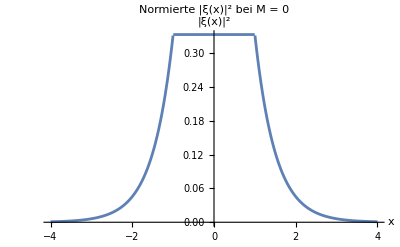

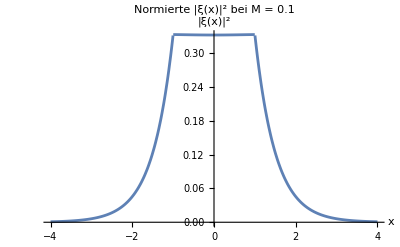

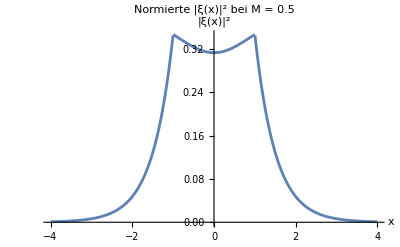

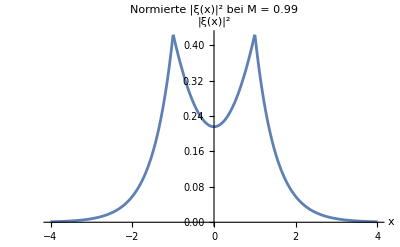

```mathematica
MagnetisierungTestsWellefunktionen={0,0.1,0.5,0.99};
ϵValue=0.1;
PlotsWellenfunktionen={};
For[i=1,i<=Length[MagnetisierungTestsWellefunktionen],i++,
plot=Plot[Evaluate[Nσ1Conj[x,ϵValue,1,MagnetisierungTestsWellefunktionen[[i]],1,1,1,1,1,1].Nσ1[x,ϵValue,1,MagnetisierungTestsWellefunktionen[[i]],1,1,1,1,1,1]],
{x,-4,4},
PlotLabel->"Normierte |ξ(x)|^2 bei M = "<>ToString[MagnetisierungTestsWellefunktionen[[i]]],
AxesLabel->{"x","|ξ(x)|^2"}];
AppendTo[PlotsWellenfunktionen,plot];
Print[plot]
]
(*GraphicsRow[PlotsWellenfunktionen,ImageSize->Full]*)
```

Matrixelemente numerisch berechnen:

Die Matrix-Multiplikation der diagonal Elemente ist jetzt bei M>0 nicht mehr selber 0, sondern die diagonal Elemente werden erst durch die Antisymmetrie im Integral 0.

```mathematica
Nσ1σ1[x_,ϵ_,L_,M_,Δ_,μN_,μSL_,μSR_,v_,ℏ_]:=Nσ1Conj[x,ϵ,L,M,Δ,μN,μSL,μSR,v,ℏ].σyτz.Nσ1[x,ϵ,L,M,Δ,μN,μSL,μSR,v,ℏ];
Nσ1σ2[x_,ϵ_,L_,M_,Δ_,μN_,μSL_,μSR_,v_,ℏ_]:=Nσ1Conj[x,ϵ,L,M,Δ,μN,μSL,μSR,v,ℏ].σyτz.Nσ2[x,ϵ,L,M,Δ,μN,μSL,μSR,v,ℏ];
Nσ2σ1[x_,ϵ_,L_,M_,Δ_,μN_,μSL_,μSR_,v_,ℏ_]:=Nσ2Conj[x,ϵ,L,M,Δ,μN,μSL,μSR,v,ℏ].σyτz.Nσ1[x,ϵ,L,M,Δ,μN,μSL,μSR,v,ℏ];
Nσ2σ2[x_,ϵ_,L_,M_,Δ_,μN_,μSL_,μSR_,v_,ℏ_]:=Nσ2Conj[x,ϵ,L,M,Δ,μN,μSL,μSR,v,ℏ].σyτz.Nσ2[x,ϵ,L,M,Δ,μN,μSL,μSR,v,ℏ];

Nσ1σ1[1.5,0.1,1,1,1,1,1,1,1,1]
Nσ1σ2[1.5,0.1,1,1,1,1,1,1,1,1]
Nσ2σ1[1.5,0.1,1,1,1,1,1,1,1,1]
Nσ2σ2[1.5,0.1,1,1,1,1,1,1,1,1]
```

0.0612805+0. ⅈ

0.00170618-0.0863603 ⅈ

0.00170618+0.0863603 ⅈ

0.0612805+0. ⅈ

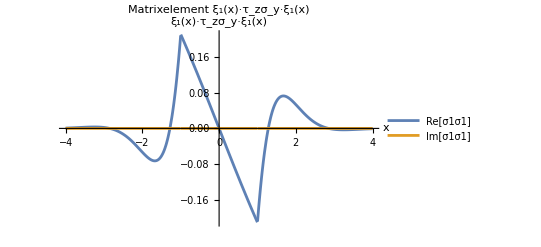

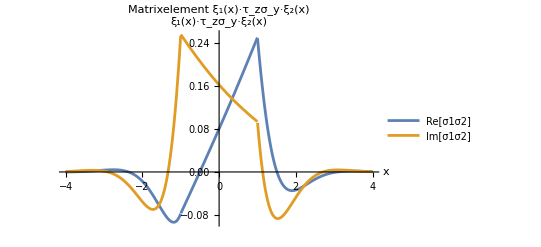

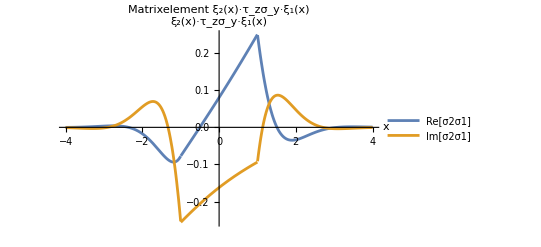

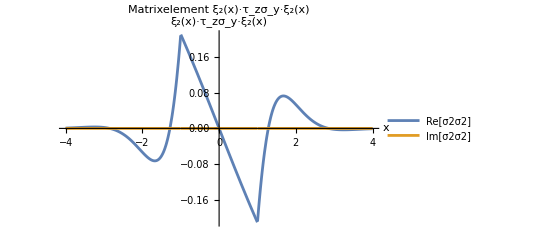

```mathematica
Plot[Evaluate[{Re[Nσ1σ1[x,0.1,1,1,1,1,1,1,1,1]],Im[Nσ1σ1[x,0.1,1,1,1,1,1,1,1,1]]}],{x,-4,4},PlotLegends->{"Re[σ1σ1]","Im[σ1σ1]"}, PlotRange->Full,PlotLabel->"Matrixelement ξ_1(x)·τ_zσ_y·ξ_1(x)",AxesLabel->{"x","ξ_1(x)·τ_zσ_y·ξ_1(x)"}]
Plot[Evaluate[{Re[Nσ1σ2[x,0.1,1,1,1,1,1,1,1,1]],Im[Nσ1σ2[x,0.1,1,1,1,1,1,1,1,1]]}],{x,-4,4},PlotLegends->{"Re[σ1σ2]","Im[σ1σ2]"}, PlotRange->Full,PlotLabel->"Matrixelement ξ_1(x)·τ_zσ_y·ξ_2(x)",AxesLabel->{"x","ξ_1(x)·τ_zσ_y·ξ_2(x)"}]
Plot[Evaluate[{Re[Nσ2σ1[x,0.1,1,1,1,1,1,1,1,1]],Im[Nσ2σ1[x,0.1,1,1,1,1,1,1,1,1]]}],{x,-4,4},PlotLegends->{"Re[σ2σ1]","Im[σ2σ1]"}, PlotRange->Full,PlotLabel->"Matrixelement ξ_2(x)·τ_zσ_y·ξ_1(x)",AxesLabel->{"x","ξ_2(x)·τ_zσ_y·ξ_1(x)"}]
Plot[Evaluate[{Re[Nσ2σ2[x,0.1,1,1,1,1,1,1,1,1]],Im[Nσ2σ2[x,0.1,1,1,1,1,1,1,1,1]]}],{x,-4,4},PlotLegends->{"Re[σ2σ2]","Im[σ2σ2]"}, PlotRange->Full,PlotLabel->"Matrixelement ξ_2(x)·τ_zσ_y·ξ_2(x)",AxesLabel->{"x","ξ_2(x)·τ_zσ_y·ξ_2(x)"}]
```

```mathematica
matrixElement11Step1[ϵ_,L_,M_,Δ_,μN_,μSL_,μSR_,v_,ℏ_]:=NIntegrate[Nσ1σ1[x,ϵ,L,M,Δ,μN,μSL,μSR,v,ℏ],{x,-0.8,0.8},PrecisionGoal->4,AccuracyGoal->4];
matrixElement11Step1[0.1,1,1,1,1,1,1,1,1]
matrixElement11Step2[ϵ_,L_,M_,Δ_,μN_,μSL_,μSR_,v_,ℏ_]:=NIntegrate[Nσ1σ1[x,ϵ,L,M,Δ,μN,μSL,μSR,v,ℏ],{x,-2,2},PrecisionGoal->4,AccuracyGoal->4];
matrixElement11Step2[0.1,1,1,1,1,1,1,1,1]
matrixElement11Step3[ϵ_,L_,M_,Δ_,μN_,μSL_,μSR_,v_,ℏ_]:=NIntegrate[Nσ1σ1[x,ϵ,L,M,Δ,μN,μSL,μSR,v,ℏ],{x,-10,10},PrecisionGoal->4,AccuracyGoal->4];
matrixElement11Step3[0.1,1,1,1,1,1,1,1,1]
matrixElement11Step4[ϵ_,L_,M_,Δ_,μN_,μSL_,μSR_,v_,ℏ_]:=NIntegrate[Nσ1σ1[x,ϵ,L,M,Δ,μN,μSL,μSR,v,ℏ],{x,-100,100},PrecisionGoal->4,AccuracyGoal->4];
matrixElement11Step4[0.1,1,1,1,1,1,1,1,1]
NmatrixElement11[ϵ_,L_,M_,Δ_,μN_,μSL_,μSR_,v_,ℏ_]:=matrixElement11Step3[ϵ,L,M,Δ,μN,μSL,μSR,v,ℏ]
```

-2.17465×10^-15-3.6024×10^-18 ⅈ

-2.5752×10^-15-1.59939×10^-17 ⅈ

-3.82702×10^-15-1.96382×10^-17 ⅈ

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {-0.97734}. NIntegrate obtained -0.000553304+2.8338×10^-18 ⅈ and 0.000386904 for the integral and error estimates.

-0.000553304+2.8338×10^-18 ⅈ

```mathematica
matrixElement12Step1[ϵ_,L_,M_,Δ_,μN_,μSL_,μSR_,v_,ℏ_]:=NIntegrate[Nσ1σ2[x,ϵ,L,M,Δ,μN,μSL,μSR,v,ℏ],{x,-0.8,0.8},PrecisionGoal->4,AccuracyGoal->4];
matrixElement12Step1[0.1,1,1,1,1,1,1,1,1]
matrixElement12Step2[ϵ_,L_,M_,Δ_,μN_,μSL_,μSR_,v_,ℏ_]:=NIntegrate[Nσ1σ2[x,ϵ,L,M,Δ,μN,μSL,μSR,v,ℏ],{x,-2,2},PrecisionGoal->4,AccuracyGoal->4];
matrixElement12Step2[0.1,1,1,1,1,1,1,1,1]
matrixElement12Step3[ϵ_,L_,M_,Δ_,μN_,μSL_,μSR_,v_,ℏ_]:=NIntegrate[Nσ1σ2[x,ϵ,L,M,Δ,μN,μSL,μSR,v,ℏ],{x,-10,10},PrecisionGoal->4,AccuracyGoal->4];
matrixElement12Step3[0.1,1,1,1,1,1,1,1,1]
NmatrixElement12[ϵ_,L_,M_,Δ_,μN_,μSL_,μSR_,v_,ℏ_]:=NIntegrate[Nσ1σ2[x,ϵ,L,M,Δ,μN,μSL,μSR,v,ℏ],{x,-100,100},PrecisionGoal->4,AccuracyGoal->4];
NmatrixElement12[0.1,1,1,1,1,1,1,1,1]
```

0.130742+0.263843 ⅈ

0.138733+0.279969 ⅈ

0.125319+0.25291 ⅈ

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {-0.97734}. NIntegrate obtained 0.125353+0.251831 ⅈ and 0.00143898 for the integral and error estimates.

0.125353+0.251831 ⅈ

```mathematica
matrixElement21Step1[ϵ_,L_,M_,Δ_,μN_,μSL_,μSR_,v_,ℏ_]:=NIntegrate[Nσ2σ1[x,ϵ,L,M,Δ,μN,μSL,μSR,v,ℏ],{x,-0.8,0.8},PrecisionGoal->4,AccuracyGoal->4];
matrixElement21Step1[0.1,1,1,1,1,1,1,1,1]
matrixElement21Step2[ϵ_,L_,M_,Δ_,μN_,μSL_,μSR_,v_,ℏ_]:=NIntegrate[Nσ2σ1[x,ϵ,L,M,Δ,μN,μSL,μSR,v,ℏ],{x,-2,2},PrecisionGoal->4,AccuracyGoal->4];
matrixElement21Step2[0.1,1,1,1,1,1,1,1,1]
matrixElement21Step3[ϵ_,L_,M_,Δ_,μN_,μSL_,μSR_,v_,ℏ_]:=NIntegrate[Nσ2σ1[x,ϵ,L,M,Δ,μN,μSL,μSR,v,ℏ],{x,-10,10},PrecisionGoal->4,AccuracyGoal->4];
matrixElement21Step3[0.1,1,1,1,1,1,1,1,1]
NmatrixElement21[ϵ_,L_,M_,Δ_,μN_,μSL_,μSR_,v_,ℏ_]:=NIntegrate[Nσ2σ1[x,ϵ,L,M,Δ,μN,μSL,μSR,v,ℏ],{x,-100,100},PrecisionGoal->4,AccuracyGoal->4];
NmatrixElement21[0.1,1,1,1,1,1,1,1,1]
```

0.130742-0.263843 ⅈ

0.138733-0.279969 ⅈ

0.125319-0.25291 ⅈ

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {-0.97734}. NIntegrate obtained 0.124631-0.252556 ⅈ and 0.00143898 for the integral and error estimates.

0.124631-0.252556 ⅈ

```mathematica
matrixElement22Step1[ϵ_,L_,M_,Δ_,μN_,μSL_,μSR_,v_,ℏ_]:=NIntegrate[Nσ2σ2[x,ϵ,L,M,Δ,μN,μSL,μSR,v,ℏ],{x,-0.8,0.8},PrecisionGoal->4,AccuracyGoal->4];
matrixElement22Step1[0.1,1,1,1,1,1,1,1,1]
matrixElement22Step2[ϵ_,L_,M_,Δ_,μN_,μSL_,μSR_,v_,ℏ_]:=NIntegrate[Nσ2σ2[x,ϵ,L,M,Δ,μN,μSL,μSR,v,ℏ],{x,-2,2},PrecisionGoal->4,AccuracyGoal->4];
matrixElement22Step2[0.1,1,1,1,1,1,1,1,1]
matrixElement22Step3[ϵ_,L_,M_,Δ_,μN_,μSL_,μSR_,v_,ℏ_]:=NIntegrate[Nσ2σ2[x,ϵ,L,M,Δ,μN,μSL,μSR,v,ℏ],{x,-10,10},PrecisionGoal->4,AccuracyGoal->4];
matrixElement22Step3[0.1,1,1,1,1,1,1,1,1]
matrixElement22Step4[ϵ_,L_,M_,Δ_,μN_,μSL_,μSR_,v_,ℏ_]:=NIntegrate[Nσ2σ2[x,ϵ,L,M,Δ,μN,μSL,μSR,v,ℏ],{x,-100,100},PrecisionGoal->4,AccuracyGoal->4];
matrixElement22Step4[0.1,1,1,1,1,1,1,1,1]
NmatrixElement22[ϵ_,L_,M_,Δ_,μN_,μSL_,μSR_,v_,ℏ_]:=matrixElement22Step3[ϵ,L,M,Δ,μN,μSL,μSR,v,ℏ]
```

1.02487×10^-15-4.35762×10^-18 ⅈ

4.95264×10^-16-7.83867×10^-18 ⅈ

1.90705×10^-15

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {1.07344}. NIntegrate obtained 0.000553304-2.47312×10^-18 ⅈ and 0.00234003 for the integral and error estimates.

0.000553304

```mathematica
Nρ[ϵ_,L_,M_,Δ_,μN_,μSL_,μSR_,v_,ℏ_]:={{matrixElement11Step3[ϵ,L,M,Δ,μN,μSL,μSR,v,ℏ],matrixElement12Step3[ϵ,L,M,Δ,μN,μSL,μSR,v,ℏ]},{matrixElement21Step3[ϵ,L,M,Δ,μN,μSL,μSR,v,ℏ],matrixElement22Step3[ϵ,L,M,Δ,μN,μSL,μSR,v,ℏ]}};
MatrixForm[Nρ[0.1,1,1,1,1,1,1,1,1]]
Nachkommas=1000;(*1000 -> 3 Nachkommastellen*)
NρRounded[ϵ_,L_,M_,Δ_,μN_,μSL_,μSR_,v_,ℏ_]:={{N[Round[Nρ[ϵ,L,M,Δ,μN,μSL,μSR,v,ℏ][[1,1]]*Nachkommas]/Nachkommas],N[Round[Nρ[ϵ,L,M,Δ,μN,μSL,μSR,v,ℏ][[1,2]]*Nachkommas]/Nachkommas]},{N[Round[Nρ[ϵ,L,M,Δ,μN,μSL,μSR,v,ℏ][[2,1]]*Nachkommas]/Nachkommas],N[Round[Nρ[ϵ,L,M,Δ,μN,μSL,μSR,v,ℏ][[2,2]]*Nachkommas]/Nachkommas]}};
MatrixForm[NρRounded[0.1,1,1,1,1,1,1,1,1]]
```

(-3.82702×10^-15-1.96382×10^-17 ⅈ | 0.125319+0.25291 ⅈ
0.125319-0.25291 ⅈ | 1.90705×10^-15)

(0. | 0.125+0.253 ⅈ
0.125-0.253 ⅈ | 0.)

Plot von v_eff:

```mathematica
$Assumptions=True;
cosϕSeries=Normal[Series[cosϕ[ϵ,L,M,Δ,μN,v,ℏ],{ϵ,0,5}]]; (*nur von ϵ^2 und ϵ^4 abhängig*)
ϵϕAnalytisch=Flatten[Values[Solve[cosϕSeries==Cos[ϕ],ϵ]]];
ϵϕAnalytisch/.{ϕ->π/2,L->1,v->1,Δ->1,ℏ->1,M->0.99,μN->1,μSR->1,μSL->1}
(*Plot[ϵϕAnalytisch/.{L->1,v->1,Δ->1,ℏ->1,M->0.99,μN->1,μSR->1,μSL->1},{ϕ,0,2π}]*)
ϵϕ[ϕ_,L_,M_,Δ_,μN_,v_,ℏ_]:=Evaluate[ϵϕAnalytisch[[1]]]
ϵϕ[π/2,1,0.999,1,1,1,1]
```

{-0.136395,0.136395,-0.597125,0.597125}

-0.134765

```mathematica
Lvalue=1;
Mvalue=0.99;
Δvalue=1;
μNvalue=1;
μSLvalue=1;
μSRvalue=1;
matrixElement21Step3[ϵϕ[π/2,Lvalue,Mvalue,Δvalue,μNvalue,1,1],Lvalue,Mvalue,Δvalue,μNvalue,μSLvalue,μSRvalue,1,1]
```

0.171051+0.225479 ⅈ

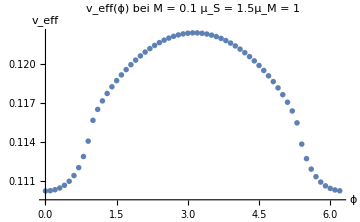

Plot 1 finished.

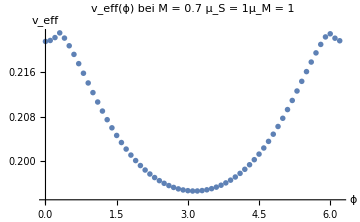

Plot 2 finished.

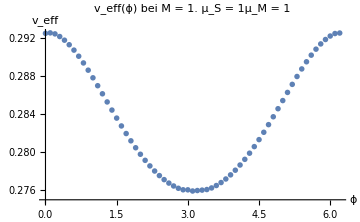

Plot 3 finished.

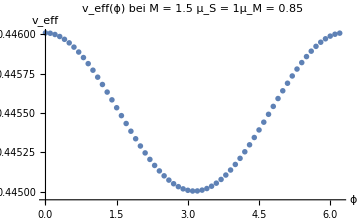

Plot 4 finished.

```mathematica
Lvalue=1;
Mvalues={0.1,0.7,0.99,1.5};
Δvalue=1;
μSvalues={1.5,1,1,1};
μNvalues={1,1,1,0.85};


Plotsveff01={};
For[i=1,i<=Length[Mvalues],i++,
punkte1=Table[{ϕ,Abs[matrixElement21Step3[ϵϕ[ϕ,Lvalue,Mvalues[[i]],Δvalue,μNvalues[[i]],1,1],Lvalue,Mvalues[[i]],Δvalue,μNvalues[[i]],μSvalues[[i]],μSvalues[[i]],1,1]]},{ϕ,0,2 π,0.1}];
plot=ListPlot[punkte1,AxesLabel->{"ϕ","v_eff"},PlotLabel->"v_eff(ϕ) bei M = "<>ToString[Round[Mvalues[[i]],0.1]]<>" μ_S = "<>ToString[μSvalues[[i]]]<>"μ_M = "<>ToString[μNvalues[[i]]],ImageSize->Medium];
AppendTo[Plotsveff01,plot];
Print[plot];
Print["Plot "<>ToString[i]<>" finished."]]
(*GraphicsRow[Plotsveff01,ImageSize->Full]*)
```

```mathematica
Mvalues={0,0.1,0.5,0.7,0.99,1.5};
μSvalues={0.1,0.2,0.5,0.8,1,1.5};
μNvalue=1;

Plotsveffgrid={};
For[i=1,i<=Length[Mvalues],i++,
PlotsRow={};
For[j=1,j<=Length[μSvalues],j++,
Print["Run "<>ToString[i]<>" - "<>ToString[j]];
punkte1=Table[{ϕ,Abs[matrixElement21Step3[ϵϕ[ϕ,Lvalue,Mvalues[[i]],Δvalue,μNvalue,1,1],Lvalue,Mvalues[[i]],Δvalue,μNvalue,μSvalues[[j]],μSvalues[[j]],1,1]]},{ϕ,0,2 π,0.1}];
Print["points "<>ToString[i]<>ToString[j]<>" finished."];
plot=ListPlot[punkte1,AxesLabel->{"ϕ","v_eff"},PlotLabel->"v_eff bei M = "<>ToString[Round[Mvalues[[i]],0.1]] <>" und μ_S = "<>ToString[Round[μSvalues[[j]],0.01]]];
Print["Plot "<>ToString[i]<>ToString[j]<>" finished."];
AppendTo[PlotsRow,plot];
];
AppendTo[Plotsveffgrid,PlotsRow]
]
GraphicsGrid[Plotsveffgrid,ImageSize->Full]
```

Run 1 - 1